# Path Finding Packet Protocols

We explore network protocols for path-finding.

## Define Graph

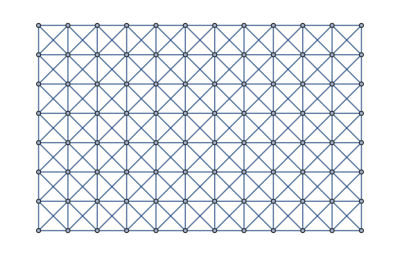

-Graphics-

```mathematica
gridDimensions={12,8};
graphVertices=CoordinateBoundsArray[{{1,gridDimensions[[1]]},{1,gridDimensions[[2]]}}]//Apply[Join];
graphVertexCoordinates=graphVertices;
graphVertexCount=graphVertices//Length;
graphVertexIndices=graphVertices//Length//Range;
graphVertexLookup=AssociationThread[graphVertices->graphVertexIndices];
graphVertexNeighborhoodVectors=CoordinateBoundsArray[{{-1,1},{-1,1}}]//Apply[Join]//ReplaceAll[{0,0}->Nothing];
graphAdjacencyMatrix=ConstantArray[0,{graphVertexCount,graphVertexCount}];
Do[
Part[graphAdjacencyMatrix,vertexIndex,
Lookup[graphVertexLookup,(graphVertexNeighborhoodVectorsᵀ+graphVertices[[vertexIndex]])ᵀ,Nothing]]=1;
,{vertexIndex,graphVertexCount}
];
graph=AdjacencyGraph[graphVertices,graphAdjacencyMatrix,VertexCoordinates->graphVertices];

graph

graph=graph//DirectedGraph
```

## Reduced Graph (Missing Edges)

```mathematica
edgeDeleteCount=120;
Manipulate[
graphReduced=
EdgeDelete[graph,
RandomSample[EdgeList[graph],edgeDeleteCount],
VertexCoordinates->GraphEmbedding[graph]
];

vertexDistances=graphReduced//UndirectedGraph//GraphDistanceMatrix//Map[Cases[_Integer]/*Max];
vertexColors=Rescale[vertexDistances];
vertexSizes=Rescale[vertexDistances]*(.5)+.1;

Graph[
graphReduced,
VertexSize->MapThread[Rule,{VertexList[graphReduced],vertexSizes}],
VertexStyle->MapThread[Rule,{VertexList[graphReduced],Map[ColorData["ThermometerColors"],vertexColors]}],
EdgeStyle->Directive[Thick,GrayLevel[.8],Arrowheads[0]],
ImageSize->Large
]

,{{edgeDeleteCount,120},0,EdgeCount[graph],1}
,TrackedSymbols:>{edgeDeleteCount}
]
```

## Enforce Bi-Directional Edges, more suitable for path-finding

-Graphics-

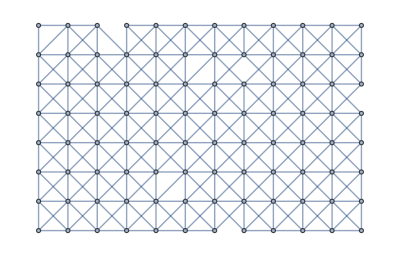

```mathematica
graphReduced=DirectedGraph@UndirectedGraph@graphReduced
graphReducedGfx=GraphPlot[UndirectedGraph@graphReduced,EdgeStyle->Opacity[0.5]]
```

## Packet Simulator - Functions

### nodeInit[]

```mathematica
nodeInit[id_]:=<|
"id"->id,
"out"->AssociationThread[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}},Null],
"in"->AssociationThread[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1},{1,-1}},Null],
"queue"->{},
"history"->{}
|>
```

### checkPort[]

```mathematica
checkPort[nodeA_,nodeB_]:=MemberQ[EdgeList[graphReduced],DirectedEdge[nodeA,nodeB]];
```

### simUpdate[]

These are some options used in simUpdate[] which control different optimizations in the path-finding algorithm.

```mathematica
$DeleteRedundantPathScoutQueue=False;
$DeleteRedundantPathScoutNode=False;
```

simUpdate[] modifies the variable nodeList and assumes the data is properly formatted as a list of nodes

```mathematica
simUpdate["Input"]:=
Module[{nodeId,packet,queue},
(* all nodes receive packets on incoming ports and add them to their queue *)
Do[
Do[
packet=nodeList[nodeId,"in",portId];
If[Not[SameQ[packet,Null]],
nodeList[nodeId,"in",portId]=Null;
AppendTo[nodeList[nodeId,"queue"],packet];
];
,{portId,RandomSample@Keys[nodeList[nodeId,"in"]]}];
,{nodeId,RandomSample@Keys[nodeList]}];
];

simUpdate["Output"]:=
Module[{nodeId,packet,queue},
(* move packets on outgoing ports to their corresponding incoming points on the receving node *)
Do[
Do[
If[Not[SameQ[nodeList[nodeId,"out",portId],Null]],
packet=nodeList[nodeId,"out",portId];
nodeList[nodeId,"out",portId]=Null;
If[checkPort[nodeId,nodeId+portId],
nodeList[nodeId+portId,"in",Minus[portId]]=packet;
,
(*Print["packet dropped!!!"];*)
];
];
,{portId,RandomSample@Keys[nodeList[nodeId,"out"]]}];
,{nodeId,RandomSample@Keys[nodeList]}];
];

simUpdate["Queue"]:=
Module[{nodeId,packet,queue},
(* all nodes process the first packet in their queue *)
Do[
If[Positive[Length[nodeList[nodeId,"queue"]]],
packet=First[nodeList[nodeId,"queue"]];
nodeList[nodeId,"queue"]=Rest[nodeList[nodeId,"queue"]];

If[packet["protocol"]=="RandomWalk",
If[Positive[packet["timeout"]],
Do[
AppendTo[packet["history"],nodeId];
Decrement[packet["timeout"]];
nodeList[nodeId,"out",outPort]=packet;
,{outPort,RandomSample[Keys[nodeList[nodeId,"out"]],3]}];
];
];

If[packet["protocol"]=="PathReturn",
If[And[Unequal[packet["source"],nodeId],Positive[Length[packet["route"]]]],
Module[{outPort},
outPort=Subtract[First[packet["route"]],nodeId];
packet["route"]=Rest[packet["route"]];
AppendTo[packet["history"],nodeId];
(*Print[packet];*)
nodeList[nodeId,"out",outPort]=packet;
];
];
];

If[packet["protocol"]=="Path",
If[Positive[Length[packet["route"]]],
Module[{outPort},
outPort=Subtract[First[packet["route"]],nodeId];
packet["route"]=Rest[packet["route"]];
AppendTo[packet["history"],nodeId];
(*Print[packet];*)
nodeList[nodeId,"out",outPort]=packet;
];
];
];

If[packet["protocol"]=="CircleScout",
If[Positive[Length[packet["route"]]],
Module[{outPort},
outPort=Subtract[First[packet["route"]],nodeId];
packet["route"]=Rest[packet["route"]];
AppendTo[packet["history"],nodeId];
(*Print[packet];*)
nodeList[nodeId,"out",outPort]=packet;
If[$CircleScoutReturnPackets,sendPathPacket[nodeId,packet["source"]];]
];
];
];

If[packet["protocol"]=="PathScout",
(* record packet signature for future reference at this node *)
If[$DeleteRedundantPathScoutNode,
If[MemberQ[nodeList[nodeId,"history"],packet[[{"protocol","source","target"}]]],
nodeList[nodeId,"queue"]=
Select[
nodeList[nodeId,"queue"],
Function[queuePacket,Unequal[queuePacket[[{"protocol","source","target"}]],packet[[{"protocol","source","target"}]]]]
];
Continue[];
,
AppendTo[nodeList[nodeId,"history"],packet[[{"protocol","source","target"}]]];
];
];

(* copy to all out ports except possibly the packet's port of entry *)
If[Equal[packet["target"],nodeId],
Module[{outPort},
outPort=Subtract[Last[packet["history"]],nodeId];
AppendTo[packet["history"],nodeId];
packet["protocol"]="PathReturn";
packet["path"]=packet["history"];
packet["route"]=Drop[Reverse[packet["history"]],2];
nodeList[nodeId,"out",outPort]=packet;
];
,
(* delete redundant PathScouts*)
If[$DeleteRedundantPathScoutQueue,
nodeList[nodeId,"queue"]=
Select[
nodeList[nodeId,"queue"],
Function[queuePacket,Unequal[queuePacket[[{"protocol","source","target"}]],packet[[{"protocol","source","target"}]]]]
];
];
If[Positive[packet["timeout"]],
Module[{outPorts,inPort},
outPorts=Keys[nodeList[nodeId,"out"]];
If[Positive[Length[packet["history"]]],
inPort=Subtract[Last[packet["history"]],nodeId];
outPorts=Complement[outPorts,{inPort}];
outPorts=Select[outPorts,FreeQ[packet["history"],nodeId+#]&];
];
outPorts=Select[outPorts,checkPort[nodeId,nodeId+#]&];
AppendTo[packet["history"],nodeId];
Decrement[packet["timeout"]];
Do[
nodeList[nodeId,"out",outPort]=packet;
,{outPort,outPorts}];
];
];
];
];
];
,{nodeId,RandomSample[Keys[nodeList]]}];
]
```

```mathematica
simUpdate[]:=
Module[{},
simUpdate["Input"];
simUpdate["Output"];
simUpdate["Queue"];
]
```

### simGraphics[]

```mathematica
simGraphics[]:=
Module[{packet,gfxPackets},
gfxPackets={};
Do[


Module[{arrow},
(* plot incoming packets *)
Do[
packet=nodeList[nodeId,"in",inPortId];
If[Not[SameQ[packet,Null]],
arrow=Arrow[{nodeId+(.5)inPortId,nodeId}];
If[packet["protocol"]=="PathReturn",
AppendTo[gfxPackets,{
Lighter[Red],AbsoluteThickness[2],Line[packet["path"]],
Darker[Red],arrow,EdgeForm[{Thick,Black}],
Disk[nodeId+(.3)inPortId,.1]
}];
,
AppendTo[gfxPackets,{Opacity[1],arrow}];
];
If[Or[packet["protocol"]=="Path",packet["protocol"]=="CircleScout"],
AppendTo[gfxPackets,{
Lighter[Red],AbsoluteThickness[2],Line[packet["history"]],
Darker[Red],arrow,EdgeForm[{Thick,Black}],
Disk[nodeId+(.3)inPortId,.1]
}];
,
AppendTo[gfxPackets,{Opacity[1],arrow}];
];
];
,{inPortId,Keys[nodeList[nodeId,"in"]]}];

(* plot outgoing packets *)
Do[
packet=nodeList[nodeId,"out",outPortId];
If[Not[SameQ[packet,Null]],
arrow=Arrow[{nodeId,nodeId+(.5)outPortId}];
If[packet["protocol"]=="PathReturn",
AppendTo[gfxPackets,{
Red,AbsoluteThickness[2],Line[packet["path"]],
Darker[Red],arrow,
EdgeForm[{Thick,Black}],Disk[nodeId+(.2)outPortId,.1]
}];
,
AppendTo[gfxPackets,{Opacity[1],arrow}];
];
If[Or[packet["protocol"]=="Path",packet["protocol"]=="CircleScout"],
AppendTo[gfxPackets,{
Red,AbsoluteThickness[2],Line[packet["history"]],
Darker[Red],arrow,
EdgeForm[{Thick,Black}],Disk[nodeId+(.2)outPortId,.1]
}];
,
AppendTo[gfxPackets,{Opacity[1],arrow}];
];
];
,{outPortId,Keys[nodeList[nodeId,"in"]]}];
];

Module[{queueLength=Length[nodeList[nodeId,"queue"]]},
If[Positive[queueLength],
AppendTo[gfxPackets,
Table[
{If[nodeList[[Key[nodeId],"queue",queueId,"protocol"]]=="PathReturn",Darker[Red],Gray],
EdgeForm[{Thick,Black}],Disk[nodeId+queueId*.015{-1,5},.1]}
,{queueId,1,queueLength}]];
];
];

,{nodeId,ReverseSortBy[Keys[nodeList],Last]}];
Return[gfxPackets];
];
```

### graphReducedGfx

```mathematica
graphReducedGraphics=GraphPlot[UndirectedGraph@graphReduced,EdgeStyle->Opacity[0.5]]
```

-Graphics-

### simPlot[]

```mathematica
simPlot[]:=
Show[
graphReducedGraphics,
Graphics[{Arrowheads[.02],simGraphics[]}],
PlotRange->{{0,13},{0,9}},
ImageSize->512
]
```

### makePathPacket[s, t]

```mathematica
makePathPacket[source_,target_]:=
<|
"id"->1,
"protocol"->"Path",
"source"->source,
"target"->target,
"history"->{},
"route"->Rest[FindShortestPath[graphReduced,source,target]],
"timeout"->128
|>;
```

### sendPathPacket[s, t]

```mathematica
sendPathPacket[source_,target_]:=
AppendTo[nodeList[source,"queue"],makePathPacket[source,target]]
```

## Packet Simulator - Execute

### experiment 1 - no optimizations

Set global variables

```mathematica
$DeleteRedundantPathScoutQueue=False;
$DeleteRedundantPathScoutNode=False;
```

define initial packet

```mathematica
packet=<|
"id"->1,
"protocol"->"PathScout",
"source"->{1,4},
"target"->{3,8},
"history"->{},
"route"->{},
"timeout"->4
|>;
```

initialize simulation (nodeList, with inserted packet)

```mathematica
nodeList=AssociationThread[VertexList[graphReduced],nodeInit/@VertexList[graphReduced]];
nodeList[packet["source"],"in",{-1,0}]=packet;
(*nodeList[packet2["source"],"in",{-1,0}]=packet2;*)
```

execute simulation loop

```mathematica
plot=simPlot[];
animationFrames={};
Monitor[
Do[
simUpdate[];
plot=simPlot[];
AppendTo[animationFrames,plot];
Pause[.1];
,{50}]
,plot]
```

### experiment 2 - delete redundant packet from each queue (taking the first in the queue)

Set global variables

```mathematica
$DeleteRedundantPathScoutQueue=True;
$DeleteRedundantPathScoutNode=False;
```

define initial packet

```mathematica
packet=<|
"id"->1,
"protocol"->"PathScout",
"source"->{1,4},
"target"->{12,8},
"history"->{},
"route"->{},
"timeout"->13
|>;
```

initialize simulation (nodeList, with inserted packet)

```mathematica
nodeList=AssociationThread[VertexList[graphReduced],nodeInit/@VertexList[graphReduced]];
nodeList[packet["source"],"in",{-1,0}]=packet;
plot=simPlot[];
(*nodeList[packet2["source"],"in",{-1,0}]=packet2;*)
```

execute simulation loop

```mathematica
plot=simPlot[];
animationFrames={};
Monitor[
Do[
simUpdate[];
plot=simPlot[];
AppendTo[animationFrames,plot];
Pause[.1];
,{50}]
,plot]
```

### experiment 3 - nodes remember which scout packets it has seen, and deletes any future redundant packets

Set global variables

```mathematica
$DeleteRedundantPathScoutQueue=True;
$DeleteRedundantPathScoutNode=True;
```

define initial packet

```mathematica
packet=<|
"id"->1,
"protocol"->"PathScout",
"source"->{1,4},
"target"->{12,8},
"history"->{},
"route"->{},
"timeout"->20
|>;
```

initialize simulation (nodeList, with inserted packet)

```mathematica
nodeList=AssociationThread[VertexList[graphReduced],nodeInit/@VertexList[graphReduced]];
nodeList[packet["source"],"in",{-1,0}]=packet;
(*nodeList[packet2["source"],"in",{-1,0}]=packet2;*)
```

execute simulation loop

```mathematica
plot=simPlot[];
animationFrames={};
Monitor[
Do[
simUpdate[];
plot=simPlot[];
AppendTo[animationFrames,plot];
Pause[.1];
,{50}]
,plot]
```

### experiment 4 - path (layer 1 circuit)

Set global variables

```mathematica
$DeleteRedundantPathScoutQueue=False;
$DeleteRedundantPathScoutNode=False;
```

define initial packet

```mathematica
packet=<|
"id"->1,
"protocol"->"Path",
"source"->{4,4},
"target"->{0,0},
"history"->{},
"route"->{{4,5},{5,5},{5,4},{5,3},{4,3},{3,3},{3,4},{3,5},{4,5},{4,4}},
"timeout"->4
|>;
```

initialize simulation (nodeList, with inserted packet)

```mathematica
nodeList=AssociationThread[VertexList[graphReduced],nodeInit/@VertexList[graphReduced]];
nodeList[packet["source"],"in",{-1,0}]=packet;
(*nodeList[packet2["source"],"in",{-1,0}]=packet2;*)
```

execute simulation loop

```mathematica
plot=simPlot[];
animationFrames={plot};
Monitor[
Do[
simUpdate[];
plot=simPlot[];
AppendTo[animationFrames,plot];
Pause[.1];
,{30}]
,plot]
```

### experiment 5 - path (layer 2 circuit)

Set global variables

```mathematica
$DeleteRedundantPathScoutQueue=False;
$DeleteRedundantPathScoutNode=False;
$CircleScoutReturnPackets=False;
```

define initial packet

```mathematica
packet=<|
"id"->1,
"protocol"->"CircleScout",
"source"->{4,4},
"target"->{0,0},
"history"->{},
"route"->{{4,5},{4,6},{5,6},{6,6},{6,5},{6,4},{6,3},{6,2},{5,2},{4,2},{3,2},{2,2},{2,3},{2,4},{2,5},{2,6},{3,6},{4,6},{4,5},{4,4}},
"timeout"->32
|>;
```

initialize simulation (nodeList, with inserted packet)

```mathematica
nodeList=AssociationThread[VertexList[graphReduced],nodeInit/@VertexList[graphReduced]];
nodeList[packet["source"],"in",{-1,0}]=packet;

sendPathPacket[{2,2},{10,3}];

plot=simPlot[];
(*nodeList[packet2["source"],"in",{-1,0}]=packet2;*)
```

execute simulation loop

```mathematica
plot//Dynamic
```

```mathematica
Do[
simUpdate["Input"];
plot=simPlot[];
Pause[0.1];

simUpdate["Output"];
plot=simPlot[];
Pause[0.1];

simUpdate["Queue"];
plot=simPlot[];
Pause[0.1];
,{50}]
```

```mathematica
simUpdate["Input"];
plot=simPlot[];
```

```mathematica
simUpdate["Output"];
plot=simPlot[];
```

```mathematica
simUpdate["Queue"];
plot=simPlot[];
```

```mathematica
plot=simPlot[];
animationFrames={plot};
Monitor[
Do[
simUpdate[];
plot=simPlot[];
AppendTo[animationFrames,plot];
Pause[.1];
,{50}]
,plot]
```